# Stably Wick Relaxing

## Initialisation

```mathematica
ClearAll["Global`*"]
```

## Introduction

### The problem

Wick relaxation gives a good (and often, fast) convergence to the ground-state, though Wick rotation yields a non-unitary Schrodinger equation; solutions break normalisation and rush to zero. Normalising once (at the end) causes precision problems in the numerical integration, and can cause numerical instability within the simulation.

### The solution

Normalisation should occur at every time-step, or some regular interval. I want to avoid coding my own numerical method; I’ll re-simulate until energy convergence is achieved

This can be more elegantly done, using ... 
• WhenEvent to halt once converged
• EvaluationMonitor or StepMonitor to check the normalisation each time-step
• NDSolve State information

```mathematica
relaxWavefunction::usage = 
	"Relaxes a given wavefunction in a given potential (both interpolated or analytic), returning full evolution";

relaxWavefunction[psi_, potential_, {x_, xL_, xR_}, duration_] :=
	NDSolveValue[
		{
			-Derivative[0,1][ψ][x, t] ==  -Derivative[2,0][ψ][x, t] / 2 + ψ[x, t] potential,
			ψ[x, 0] == psi,
			ψ[xL, t] == 0,
			ψ[xR, t] == 0
		},
		ψ, {x, xL, xR}, {t, 0, duration}
	]
```

```mathematica
initialWavefunction::usage =
	"Returns a flat, analytic, initial wavefunction for wick relaxation";

initialWavefunction[{x_, xL_, xR_}] :=
	normaliseWavefunction[
		UnitStep[x - (xL+0.01)] - UnitStep[x - (xR-0.01)],
		{x, xL, xR}
	]
	
normaliseWavefunction[psi_, domain_:{x, -∞, ∞}] :=
	psi / Sqrt[NIntegrate[
		Abs[psi]^2,
		domain,
		Method -> {Automatic, "SymbolicProcessing" -> 0}
	]]
```

```mathematica
hamiltonian[psi_, potential_, r_:x] := 
	-1/2 D[psi, {r,2}] + potential psi
	
expectedEnergy[psi_, potential_,  domain_:{x, -∞, ∞}] :=
	With[
		{r = domain[[1]]},
		NIntegrate[
			(Conjugate[psi] /. Conjugate[r] -> r)
			(hamiltonian[psi, potential, r]),
			domain,
			Method->{Automatic, "SymbolicProcessing" ->0}
		]
	]


getGroundstate::usage = 
	"Returns the groundstate of a given potential (analytic or interpolated), found through Wick 
	relaxation by repeatedly performing NDSolve for duration timestep until TraditionalForm`";

getGroundstate[potential_, domain_:{x, -5, 5}, timestep_:0.1, threshold_:0.01] :=
	Module[
		{x, psi, prevE, curE},
		x = domain[[1]];
		psi = initialWavefunction[domain];
		prevE = expectedEnergy[psi, potential, domain];
		
		psi = relaxWavefunction[psi, potential, domain, timestep][x, timestep];
		psi = normaliseWavefunction[psi, domain];
		curE = expectedEnergy[psi, potential, domain];
		
		While[
			Abs[(curE - prevE)/(curE timestep)] > threshold,
			prevE = curE;
			psi = relaxWavefunction[psi, potential, domain, timestep][x, timestep];
			psi = normaliseWavefunction[psi, domain];
			curE = expectedEnergy[psi, potential, domain];
		];
		
		psi
	]
	
(* Evaluate suggestion from here: 
	https://mathematica.stackexchange.com/questions/29812/interpolating-function-inside-of-ndsolve *)
	
(* possible fix (interpolate back to table back to interpolate) here:
https://mathematica.stackexchange.com/questions/56964/problem-when-defining-function-through-nintegrate-and-ndsolve-and-interpolation 
*)
```

```mathematica
getGroundstate[1/2 x^2]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
testinterp = relaxWavefunction[initialWavefunction[{x, -5, 5}], 1/2 x^2, {x, -5, 5}, 0.01]
lastval = testinterp[x, 0.01]
```

InterpolatingFunction[{{-5., 5.}, {0., 0.01}}, <>]

InterpolatingFunction[{{-5., 5.}, {0., 0.01}}, <>][x,0.01]

```mathematica
testinterp["Methods"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid}

```mathematica
anotherfunc[x_] = ListInterpolation[Table[lastval, {x, -5, 5, 0.01}], {{-5, 5}}, Method->"Spline"][x];
```

```mathematica
FunctionInterpolation[testinterp[r, 0.01], {r, -5, 5}];
```

FunctionInterpolation::precbd: Requested precision ∞ is not a machine-sized real number between $MinPrecision and $MaxPrecision.

```mathematica
Length[testinterp["Grid"]]
```

25

```mathematica
refreshInterpolator[func_, duration_] :=
	With[
		{grid = PropertyValue[func, "Coordinates"][[1]]},
		Interpolation[MapThread[({#1,#2}&), grid, (func[#,duration]&) @ grid], Method->"Spline"]
	]
```

```mathematica
refreshInterpolator[testinterp, 0.01]
```

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[«1»].

Interpolation::innd: First argument in MapThread[«1»] does not contain a list of data and coordinates.

Interpolation[MapThread[{#1,#2}&,{-5.,-4.58333,-4.16667,-3.75,-3.33333,-2.91667,-2.5,-2.08333,-1.66667,-1.25,-0.833333,-0.416667,0.,0.416667,0.833333,1.25,1.66667,2.08333,2.5,2.91667,3.33333,3.75,4.16667,4.58333,5.},{0.,0.278045,0.290461,0.294769,0.299131,0.303052,0.306491,0.309432,0.311858,0.313759,0.315124,0.315945,0.31622,0.315945,0.315124,0.313759,0.311858,0.309432,0.306491,0.303052,0.299131,0.294769,0.290461,0.278045,0.}],Method→Spline]

```mathematica
(testinterp[#, 0.01]&) @ PropertyValue[testinterp, "Coordinates"][[1]]
```

{0.,0.278045,0.290461,0.294769,0.299131,0.303052,0.306491,0.309432,0.311858,0.313759,0.315124,0.315945,0.31622,0.315945,0.315124,0.313759,0.311858,0.309432,0.306491,0.303052,0.299131,0.294769,0.290461,0.278045,0.}

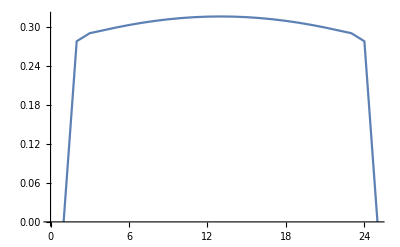

```mathematica
ListLinePlot[%]
```

```mathematica
#^2& @ {1, 2, 3}
```

{1,4,9}

```mathematica
PropertyValue[testinterp, "Coordinates"][[1]]
```

{-5.,-4.58333,-4.16667,-3.75,-3.33333,-2.91667,-2.5,-2.08333,-1.66667,-1.25,-0.833333,-0.416667,0.,0.416667,0.833333,1.25,1.66667,2.08333,2.5,2.91667,3.33333,3.75,4.16667,4.58333,5.}

```mathematica
PropertyValue[testinterp, "Coordinates"][[1]]
```

```mathematica
PropertyValue[testinterp, "ValuesOnGrid"][[All, -1]]
```

{0.,0.278045,0.290461,0.294769,0.299131,0.303052,0.306491,0.309432,0.311858,0.313759,0.315124,0.315945,0.31622,0.315945,0.315124,0.313759,0.311858,0.309432,0.306491,0.303052,0.299131,0.294769,0.290461,0.278045,0.}

```mathematica
ListLinePlot[%]
```

-Graphics-

```mathematica
Plot[testinterp[x, 0.01], {x, -5, 5}, PlotRange->{0,0.35}]
```

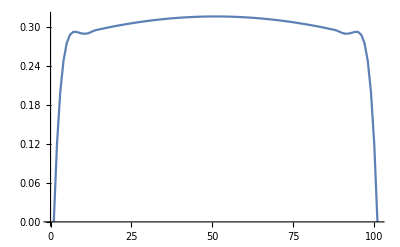

```mathematica
ListLinePlot[ testinterp[#, 0.01]& @  Range[-5, 5,0.1]]
```

```mathematica
PropertyValue[testinterp, "ValuesOnGrid"]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.316228,0.315815,0.315403,0.311361,0.307372,0.303437,0.299555,0.295724,0.291945,0.288215,0.284536,0.281271,0.278045},{0.316228,0.315958,0.315688,0.313031,0.310394,0.307775,0.305175,0.302593,0.300029,0.297484,0.294957,0.292702,0.290461},{0.316228,0.316003,0.315778,0.313565,0.311369,0.309188,0.307023,0.304873,0.302738,0.300619,0.298514,0.296636,0.294769},{0.316228,0.31605,0.315872,0.314122,0.312381,0.31065,0.308929,0.307216,0.305514,0.30382,0.302136,0.30063,0.299131},{0.316228,0.316092,0.315955,0.314614,0.313279,0.311949,0.310624,0.309305,0.307991,0.306683,0.30538,0.304214,0.303052},{0.316228,0.316128,0.316028,0.315041,0.314058,0.313078,0.312101,0.311126,0.310154,0.309186,0.30822,0.307354,0.306491},{0.316228,0.316158,0.316089,0.315403,0.314719,0.314037,0.313355,0.312675,0.311997,0.311319,0.310643,0.310037,0.309432},{0.316228,0.316183,0.316139,0.3157,0.315261,0.314823,0.314386,0.313949,0.313512,0.313076,0.31264,0.312249,0.311858},{0.316228,0.316203,0.316178,0.315931,0.315684,0.315437,0.31519,0.314943,0.314696,0.314449,0.314203,0.313981,0.313759},{0.316228,0.316217,0.316206,0.316096,0.315986,0.315876,0.315765,0.315655,0.315544,0.315434,0.315323,0.315224,0.315124},{0.316228,0.316225,0.316222,0.316195,0.316167,0.316139,0.316111,0.316083,0.316055,0.316026,0.315997,0.315971,0.315945},{0.316228,0.316228,0.316228,0.316228,0.316227,0.316227,0.316226,0.316226,0.316225,0.316224,0.316222,0.316221,0.31622},{0.316228,0.316225,0.316222,0.316195,0.316167,0.316139,0.316111,0.316083,0.316055,0.316026,0.315997,0.315971,0.315945},{0.316228,0.316217,0.316206,0.316096,0.315986,0.315876,0.315765,0.315655,0.315544,0.315434,0.315323,0.315224,0.315124},{0.316228,0.316203,0.316178,0.315931,0.315684,0.315437,0.31519,0.314943,0.314696,0.314449,0.314203,0.313981,0.313759},{0.316228,0.316183,0.316139,0.3157,0.315261,0.314823,0.314386,0.313949,0.313512,0.313076,0.31264,0.312249,0.311858},{0.316228,0.316158,0.316089,0.315403,0.314719,0.314037,0.313355,0.312675,0.311997,0.311319,0.310643,0.310037,0.309432},{0.316228,0.316128,0.316028,0.315041,0.314058,0.313078,0.312101,0.311126,0.310154,0.309186,0.30822,0.307354,0.306491},{0.316228,0.316092,0.315955,0.314614,0.313279,0.311949,0.310624,0.309305,0.307991,0.306683,0.30538,0.304214,0.303052},{0.316228,0.31605,0.315872,0.314122,0.312381,0.31065,0.308929,0.307216,0.305514,0.30382,0.302136,0.30063,0.299131},{0.316228,0.316003,0.315778,0.313565,0.311369,0.309188,0.307023,0.304873,0.302738,0.300619,0.298514,0.296636,0.294769},{0.316228,0.315958,0.315688,0.313031,0.310394,0.307775,0.305175,0.302593,0.300029,0.297484,0.294957,0.292702,0.290461},{0.316228,0.315815,0.315403,0.311361,0.307372,0.303437,0.299555,0.295724,0.291945,0.288215,0.284536,0.281271,0.278045},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
testinterp[[2]]
```

{5,5,1,{25,13},{6,4},0,0,0,0,Automatic,{},{},False}

```mathematica
SetProperty[testinterp, Method -> "Spline"]
```

SetProperty::pouns: -- Message text not found -- (InterpolatingFunction)

SetProperty[InterpolatingFunction[{{-5., 5.}, {0., 0.01}}, <>],Method→Spline]

```mathematica
NDSolveValue[
	{
		-Derivative[0,1][ψ][x,t]==1/2 x^2 ψ[x,t]-1/2 Derivative[2,0][ψ][x,t],
		ψ[x,0]== anotherfunc[x],
		ψ[-5,t]==0,
		ψ[5,t]==0
	},
	ψ,
	{x,-5,5},
	{t, 0, 0.01}
]

Plot[Abs[%[x, 0.01]]^2, {x, -5, 5}]
```

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolveValue[{-ψ^(0,1)[x,t]==1/2 x^2 ψ[x,t]-1/2 ψ^(2,0)[x,t],ψ[x,0]==anotherfunc[x],ψ[-5,t]==0,ψ[5,t]==0},ψ,{x,-5,5},{t,0,0.01}]

NDSolveValue::dsvar: -4.9998 cannot be used as a variable.

NDSolveValue::dsvar: -4.79571 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics-

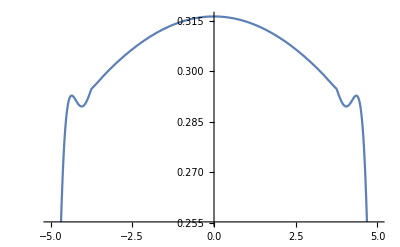

```mathematica
Plot[testinterp[x, 0.01], {x, -5, 5}]
```

1.06 InterpolatingFunction[{{-5., 5.}, {0., 0.01}}, <>][x,0.01]

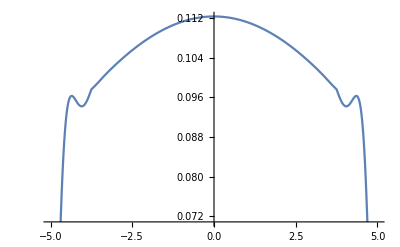

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

1.0378 InterpolatingFunction[{{-5., 5.}, {0., 0.01}}, <>][x,0.01]

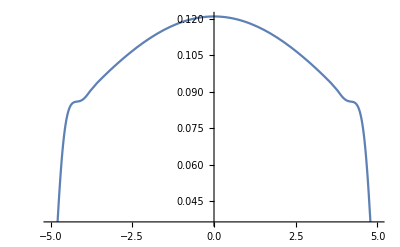

-Graphics-

```mathematica
normaliseWavefunction[[x, 0.01], {x, -5, 5}]
Plot[Abs[%]^2, {x, -5, 5}]

normaliseWavefunction[relaxWavefunction[%%, 1/2 x^2, {x, -5, 5}, 0.01][x, 0.01], {x, -5, 5}]
Plot[Abs[%]^2, {x, -5, 5}]
```

## Paul’s Elegant method

```mathematica
(* WhenEvent or Method->{"EventLocator"... } to half once converged *)
```

```mathematica
(* StepMonitor to renorm *)
```

```mathematica
(* specifying domain as region *)
```

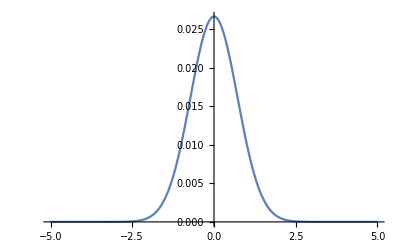

```mathematica
testingPaulsMethod[potential_, {x_, xL_, xR_}, duration_:1] :=
	NDSolveValue[
		{
			-Derivative[0,1][ψ][x, t] ==  -Derivative[2,0][ψ][x, t] / 2 + ψ[x, t] potential,
			ψ[x, 0] == initialWavefunction[{x, xL, xR}],
			ψ[xL, t] == 0,
			ψ[xR, t] == 0
		},
		ψ, {x, xL, xR}, {t, 0, duration}
	]
Plot[Abs[testingPaulsMethod[1/2 x^2, {x, -5, 5}, 2][r, 2]]^2, {r, -5, 5}]
```

Not gonna switch to Interval (awkward to pass without funcs)

```mathematica
testfunc[dom_] :=
FullForm[dom]
```

```mathematica
testfunc[x ∈ [0, 5]]
```

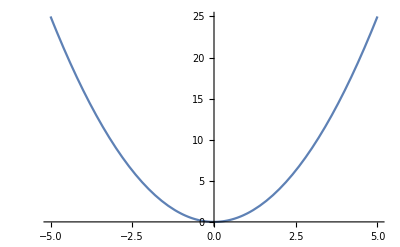

```mathematica
Plot[x^2, x ∈ Interval[{-5, 5}]]
```

```mathematica
myPlotFunc[func_, x_ ∈ domain_] :=
	Plot[
	x
```

```mathematica
myPlotFunc[func_, x_ ∈ domain_] :=
	Plot[
		func,
		x ∈ Interval[domain]
	]
```

```mathematica
myPlotFunc[x^2, x ∈ {-5, 5}]
```

-Graphics-

```mathematica
advPlotFunc[func_, vars_
```

```mathematica
{a, b} ∈ Interval[{{-5, 5}, {0, 1}}]
```

{a,b}∈Interval[{{-5,5},{0,1}}]

```mathematica
Plot3D[x^2+25 y^2, {x, -5, 5}, {y, -1, 1}]
```

-Graphics3D-

```mathematica
Plot3D[x^2+25 y^2,  x ∈ Interval[{-5, 5}], y  ∈Interval[{-1, 1}]]
```

Plot3D::idomdim: y∈Interval[{-1,1}] does not have a valid dimension as a plotting domain.

Plot3D[x^2+25 y^2,x∈Interval[{-5,5}],y∈Interval[{-1,1}]]

```mathematica
Plot3D[x^2+25 y^2, {x,y} ∈ Interval[{-5, 5}, {-1, 1}]]
```

Plot3D::idomdim: {x,y}∈Interval[{-5,5},{-1,1}] does not have a valid dimension as a plotting domain.

Plot3D[x^2+25 y^2,{x,y}∈Interval[{-5,5},{-1,1}]]

```mathematica
ClearAll[advPlotFunc, myPlotFunc]
```